```mathematica
summary=SemanticImport[FileNameJoin@{NotebookDirectory[],"list3.2.xls"}]
```

Dataset[<>]

```mathematica
summary=summary[All,;;8]//Dataset
```

Dataset[<>]

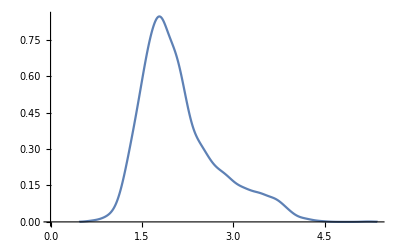

```mathematica
SmoothHistogram[Log10/@summary[All,"volume"]]
```

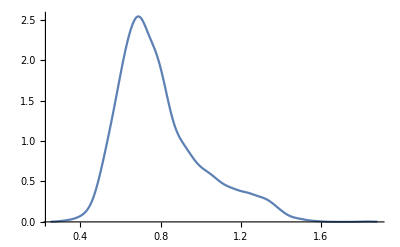

```mathematica
SmoothHistogram[Log10/@summary[All,"eq. diam."],PlotRange->All]
```

```mathematica
SmoothHistogram3D[Values/@summary[All,{"x loc.","y loc."}],AxesLabel->{"x","y"}]
```

-Graphics3D-

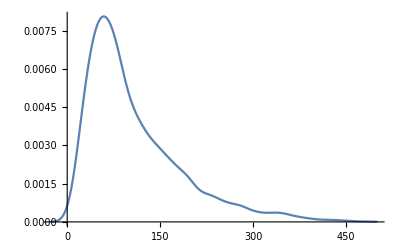

```mathematica
SmoothHistogram[summary[All,"slice no."],PlotRange->All]
```